```mathematica
(*Mathematica*)
```

```mathematica
(* empirical polyhedrons vertex x^(n*4) n Model Dodecashedrons*)
```

```mathematica
p0={-1+45 x^3-116 x^6-45 x^9-x^12,-1+137 x^4-368 x^8-137 x^12-x^16,-1+228 x^5-494 x^10-228 x^15-x^20,-1+273 x^6-620 x^12-273 x^18-x^24,-1+319 x^7-620 x^14-319 x^21-x^28,-1+365 x^8-683 x^16-365 x^24-x^32,-1+501 x^9-872 x^18-501 x^27-x^36}
```

{-1+45 x^3-116 x^6-45 x^9-x^12,-1+137 x^4-368 x^8-137 x^12-x^16,-1+228 x^5-494 x^10-228 x^15-x^20,-1+273 x^6-620 x^12-273 x^18-x^24,-1+319 x^7-620 x^14-319 x^21-x^28,-1+365 x^8-683 x^16-365 x^24-x^32,-1+501 x^9-872 x^18-501 x^27-x^36}

```mathematica
Table[CoefficientList[p0[[i]],x],{i,Length[p0]}]
```

{{-1,0,0,45,0,0,-116,0,0,-45,0,0,-1},{-1,0,0,0,137,0,0,0,-368,0,0,0,-137,0,0,0,-1},{-1,0,0,0,0,228,0,0,0,0,-494,0,0,0,0,-228,0,0,0,0,-1},{-1,0,0,0,0,0,273,0,0,0,0,0,-620,0,0,0,0,0,-273,0,0,0,0,0,-1},{-1,0,0,0,0,0,0,319,0,0,0,0,0,0,-620,0,0,0,0,0,0,-319,0,0,0,0,0,0,-1},{-1,0,0,0,0,0,0,0,365,0,0,0,0,0,0,0,-683,0,0,0,0,0,0,0,-365,0,0,0,0,0,0,0,-1},{-1,0,0,0,0,0,0,0,0,501,0,0,0,0,0,0,0,0,-872,0,0,0,0,0,0,0,0,-501,0,0,0,0,0,0,0,0,-1}}

```mathematica
w=Table[CoefficientList[p0[[i]],x][[i+3]],{i,Length[p0]}]
```

{45,137,228,273,319,365,501}

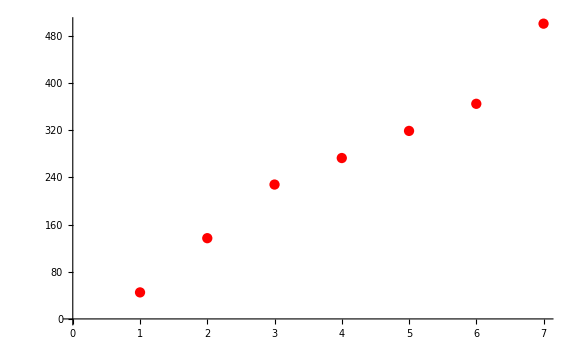

```mathematica
g0=ListPlot[w,PlotStyle->Red,ImageSize->Large]
```

```mathematica
f[x_]=Fit[w,{1,x},x]
```

-6.71429+68.3929 x

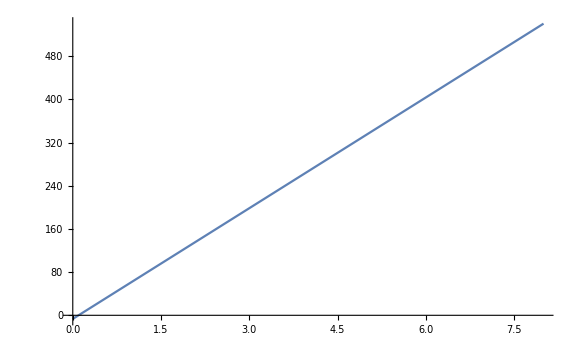

```mathematica
g1=Plot[ f[x],{x,0,Length[w]+1},ImageSize->Large]
```

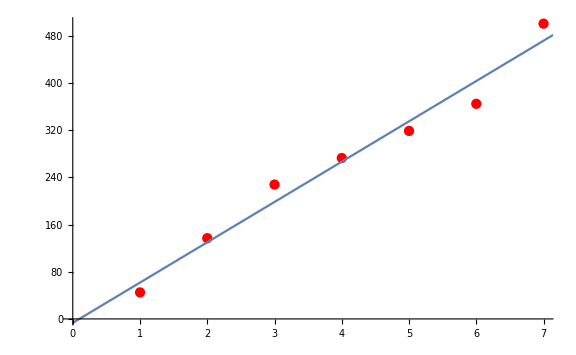

```mathematica
Show[{g0,g1}]
```

```mathematica
w1=Table[-CoefficientList[p0[[i]],x][[2*(i-1)+7]],{i,Length[p0]}]
```

{116,368,494,620,620,683,872}

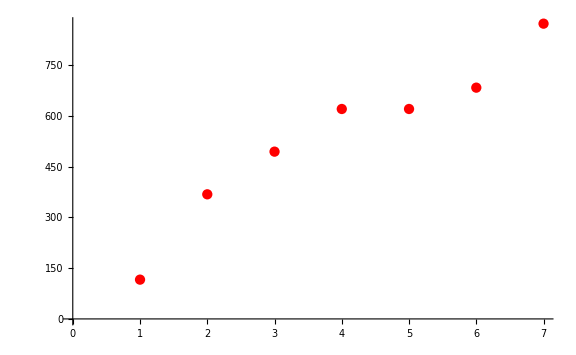

```mathematica
g2=ListPlot[w1,PlotStyle->Red,ImageSize->Large]
```

```mathematica
Clear[g]
```

```mathematica
g[x_]=Fit[w1,{1,x},x]
```

107.+108. x

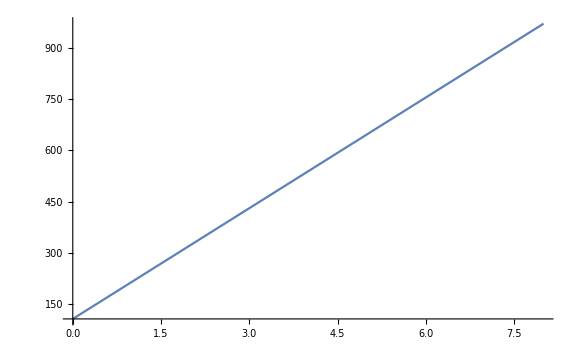

```mathematica
g3=Plot[ g[x],{x,0,Length[w]+1},ImageSize->Large]
```

```mathematica
Table[Floor[f[i]],{i,10}]
```

{61,130,198,266,335,403,472,540,608,677}

```mathematica
Table[Floor[g[i]],{i,10}]
```

{215,323,431,539,647,755,863,971,1079,1187}

```mathematica
(* Polyhedrons from line*)
```

```mathematica
Table[-1+Floor[f[i]]*x^(i+2)-Floor[g[i]]*x^(2*(i+2))-Floor[f[i]]*x^(3*(i+2))-x^(4*(i+2)),{i,10}]
```

{-1+61 x^3-215 x^6-61 x^9-x^12,-1+130 x^4-323 x^8-130 x^12-x^16,-1+198 x^5-431 x^10-198 x^15-x^20,-1+266 x^6-539 x^12-266 x^18-x^24,-1+335 x^7-647 x^14-335 x^21-x^28,-1+403 x^8-755 x^16-403 x^24-x^32,-1+472 x^9-863 x^18-472 x^27-x^36,-1+540 x^10-971 x^20-540 x^30-x^40,-1+608 x^11-1079 x^22-608 x^33-x^44,-1+677 x^12-1187 x^24-677 x^36-x^48}

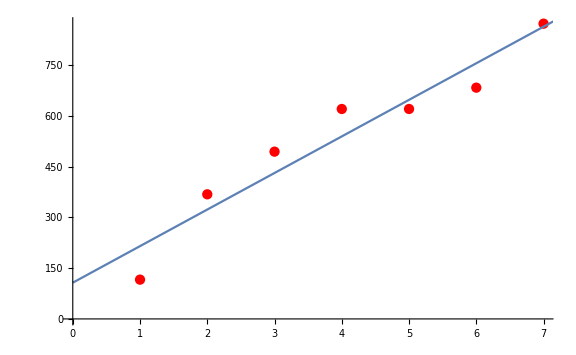

```mathematica
Show[{g2,g3}]
```

```mathematica
(*Linearized polynomials*)
```

```mathematica
Clear[f,g,fa,ga,g0,g1,g2,g3,w,w1]
```

```mathematica
(*Coefficient lines adjusted to the Dodecahedron Absolute invariant*)
```

```mathematica
f[x_]=24+68*x
```

24+68 x

```mathematica
g[x_]=170+108*x
```

170+108 x

```mathematica
p=Table[-1+Floor[f[i]]*x^(i+2)-Floor[g[i]]*x^(2*(i+2))-Floor[f[i]]*x^(3*(i+2))-x^(4*(i+2)),{i,10}]
```

{-1+92 x^3-278 x^6-92 x^9-x^12,-1+160 x^4-386 x^8-160 x^12-x^16,-1+228 x^5-494 x^10-228 x^15-x^20,-1+296 x^6-602 x^12-296 x^18-x^24,-1+364 x^7-710 x^14-364 x^21-x^28,-1+432 x^8-818 x^16-432 x^24-x^32,-1+500 x^9-926 x^18-500 x^27-x^36,-1+568 x^10-1034 x^20-568 x^30-x^40,-1+636 x^11-1142 x^22-636 x^33-x^44,-1+704 x^12-1250 x^24-704 x^36-x^48}

```mathematica
Table[CoefficientList[p0[[i]],x],{i,Length[p0]}]
```

{{-1,0,0,45,0,0,-116,0,0,-45,0,0,-1},{-1,0,0,0,137,0,0,0,-368,0,0,0,-137,0,0,0,-1},{-1,0,0,0,0,228,0,0,0,0,-494,0,0,0,0,-228,0,0,0,0,-1},{-1,0,0,0,0,0,273,0,0,0,0,0,-620,0,0,0,0,0,-273,0,0,0,0,0,-1},{-1,0,0,0,0,0,0,319,0,0,0,0,0,0,-620,0,0,0,0,0,0,-319,0,0,0,0,0,0,-1},{-1,0,0,0,0,0,0,0,365,0,0,0,0,0,0,0,-683,0,0,0,0,0,0,0,-365,0,0,0,0,0,0,0,-1},{-1,0,0,0,0,0,0,0,0,501,0,0,0,0,0,0,0,0,-872,0,0,0,0,0,0,0,0,-501,0,0,0,0,0,0,0,0,-1}}

```mathematica
w=Table[CoefficientList[p[[i]],x][[i+3]],{i,Length[p0]}]
```

{92,160,228,296,364,432,500}

```mathematica
w1=Table[-CoefficientList[p[[i]],x][[2*(i-1)+7]],{i,Length[p0]}]
```

{278,386,494,602,710,818,926}

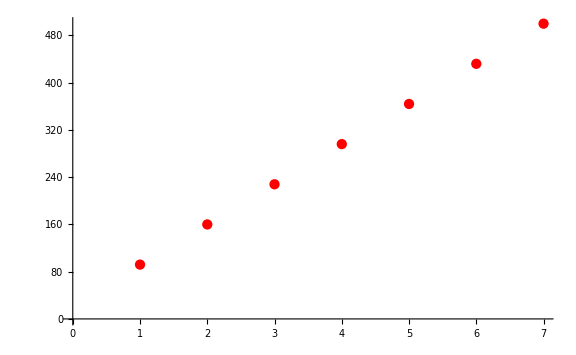

```mathematica
g0=ListPlot[w,PlotStyle->Red,ImageSize->Large]
```

```mathematica
fa[x_]=Fit[w,{1,x},x]
```

24.+68. x

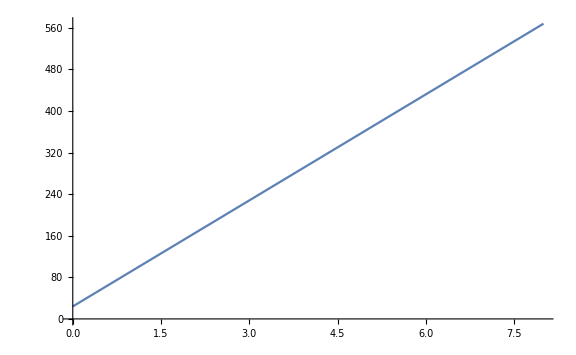

```mathematica
g1=Plot[ fa[x],{x,0,Length[w]+1},ImageSize->Large]
```

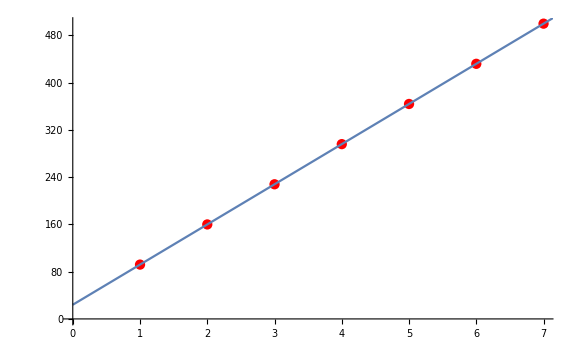

```mathematica
Show[{g0,g1}]
```

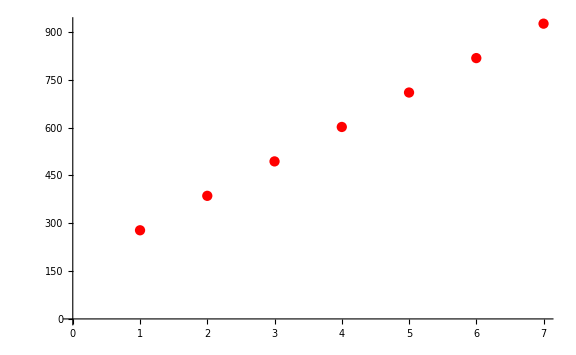

```mathematica
g2=ListPlot[w1,PlotStyle->Red,ImageSize->Large]
```

```mathematica
ga[x_]=Fit[w1,{1,x},x]
```

170.+108. x

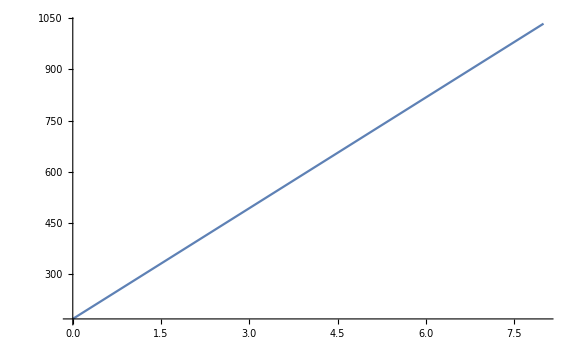

```mathematica
g3=Plot[ ga[x],{x,0,Length[w]+1},ImageSize->Large]
```

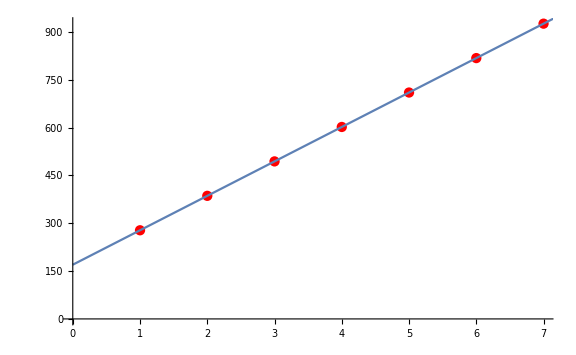

```mathematica
Show[{g2,g3}]
```

```mathematica
(* absolute elliptical invariant (rational polynomial equations) to fit the dodecahedron model*)
```

((-1+45 x^3-116 x^6-45 x^9-x^12)^3)/(432 x^3 (-1+4 x^3+x^6)^3)

((-1+137 x^4-368 x^8-137 x^12-x^16)^3)/(864 x^4 (-1+x^8+7 z^4)^4)

((-1+228 x^5-494 x^10-228 x^15-x^20)^3)/(1728 x^5 (-1+11 x^5+x^10)^5)

((-1+273 x^6-620 x^12-273 x^18-x^24)^3)/(3456 x^6 (-1+13 x^6+x^12)^6)

((-1+319 x^7-620 x^14-319 x^21-x^28)^3)/(6912 x^7 (-1+15 x^7+x^14)^7)

((-1+365 x^8-683 x^16-365 x^24-x^32)^3)/(13824 x^8 (-1+17 x^8+x^16)^8)

((-1+501 x^9-872 x^18-501 x^27-x^36)^3)/(27648 x^8 (-1+19 x^9+x^18)^9)

```mathematica
(*end*)
```

```mathematica
(*Mathematica*)
```

```mathematica
(*Convex hull Voronoi diagram program*)
<<ComputationalGeometry`
(*x36 9 model dodecahedron polynomial*)
pa[z_]=-1+500 x^9-926 x^18-500 x^27-x^36
pts=Union[{2*Re[x],2*Im[x],1-Abs[x]^2}/(1+Abs[x]^2)/.NSolve[pa[x]==0,x]]
ptsn=Table[Hue[Norm[x/.NSolve[pa[x]==0,x][[i]]]],{i,Length[pts]}];
(* Voronoi diagram*)
g1=Show[{
DiagramPlot[Most/@pts,LabelPoints->False]/._Point:>{},
Graphics[{Red,PointSize[.005],Point[Most/@pts]}]
},PlotRange->{{-2,2},{-2,2}},Frame->True,PlotRangeClipping->True,ImageSize->1000]
(* 3d projection of polyhedron*)
Show[Graphics3D[{Red,PointSize[0.0375],Point/@pts}],Axes->True]
(* convex hull: MathWorld Library*)
<<ConvexHull`
hull0=ConvexHull3D[pts];
Length[hull0]
hull1=Flatten[Table[If[i≤Length[ptsn],{ptsn[[i]],hull0[[i]]},{Hue[1],hull0[[i]]}],{i,Length[hull0]}]];
```

-1+500 x^9-926 x^18-500 x^27-x^36

{{-0.995741,0.,-0.0921904},{-0.935691,-0.340564,0.0921904},{-0.935691,0.340564,0.0921904},{-0.801463,0.,-0.598045},{-0.762782,-0.64005,-0.0921904},{-0.762782,0.64005,-0.0921904},{-0.753129,-0.274116,0.598045},{-0.753129,0.274116,0.598045},{-0.613956,-0.51517,-0.598045},{-0.613956,0.51517,-0.598045},{-0.497871,-0.862337,0.0921904},{-0.497871,0.862337,0.0921904},{-0.400731,-0.694087,0.598045},{-0.400731,0.694087,0.598045},{-0.172909,-0.980614,-0.0921904},{-0.172909,0.980614,-0.0921904},{-0.139173,-0.789287,-0.598045},{-0.139173,0.789287,-0.598045},{0.139173,-0.789287,0.598045},{0.139173,0.789287,0.598045},{0.172909,-0.980614,0.0921904},{0.172909,0.980614,0.0921904},{0.400731,-0.694087,-0.598045},{0.400731,0.694087,-0.598045},{0.497871,-0.862337,-0.0921904},{0.497871,0.862337,-0.0921904},{0.613956,-0.51517,0.598045},{0.613956,0.51517,0.598045},{0.753129,-0.274116,-0.598045},{0.753129,0.274116,-0.598045},{0.762782,-0.64005,0.0921904},{0.762782,0.64005,0.0921904},{0.801463,0.,0.598045},{0.935691,-0.340564,-0.0921904},{0.935691,0.340564,-0.0921904},{0.995741,0.,0.0921904}}

38

```mathematica
g=Graphics3D[hull={Opacity[0.5],hull1},ImageSize->1000,Boxed->False,Background->Black,ViewPoint->{3,3,3}]
```

```mathematica
Export["x36_9model_Dodecahedron_linearized.jpg",g]
```

x36_9model_Dodecahedron_linearized.jpg

```mathematica
Export["x36_9model_Dodecahedron_linearized.ply",g]
```

x36_9model_Dodecahedron_linearized.ply

```mathematica
Export["x36_9model_Dodecahedron_linearized.stl",g]
```

x36_9model_Dodecahedron_linearized.stl

```mathematica
(*end*)
```

Lookup::invrl: The argument Missing[NotAvailable] is not a valid Association or a list of rules.